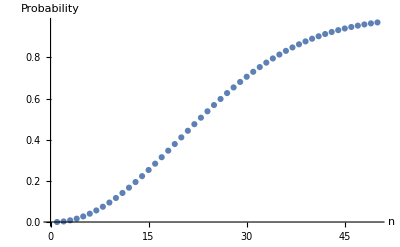

```mathematica
noshare = {{1, 1}};
share = {{1,0}};
currentnoshare = 1;
For[n = 2, n ≤ 50, n++, {
newfactor = (365 - (n-1))/365;
currentnoshare = currentnoshare * newfactor;
noshare = AppendTo[noshare, {n,1.0  currentnoshare}];
share = AppendTo[share, {n, 1.0 - currentnoshare}];
}];
Print[ListPlot[share, AxesLabel->{"n", "Probability"}]]
```